```mathematica
(* mathematica*)
(* by Roger Bagula 6 Jan 2026©*)
Clear[f,dlst,pt,cr,ptlst]

allColors=ColorData["Legacy"][[3,1]];
firstCols={"Blue","Cyan","ManganeseBlue","DodgerBlue" ,"Magenta","Purple","Pink","Tomato","Red","DarkOrange","Orange","DeepNaplesYellow","Gold","Banana","Yellow","LightYellow","Orange","Pink","LightPink","Yellow","LightYellow","LightPink","White","DeepNaplesYellow", "Orange","DarkOrange","Tomato","Red","Tomato","Pink","LightPink","DeepNaplesYellow", "Orange","DarkOrange","Tomato","White","Pink","Banana","LightBlue","DodgerBlue","Cyan","White","Purple","DarkOrchid","Magenta","ManganeseBlue","DeepNaplesYellow", "Orange","DarkOrange","Tomato","GoldOchre","LightPink","Magenta","Green","DarkOrchid","LightSalmon","LightPink","Sienna","Green","Mint","DarkSlateGray","ManganeseBlue","SlateGray","DarkOrange","MistyRose","DeepNaplesYellow","GoldOchre","SapGreen","Yellow","Yellow","Tomato","DeepNaplesYellow","DodgerBlue","Cyan","Red","Blue","DeepNaplesYellow","Green","Magenta","DarkOrchid","LightSalmon","LightPink","Sienna","Green","Mint","DarkSlateGray","ManganeseBlue","SlateGray","DarkOrange","MistyRose","DeepNaplesYellow","GoldOchre","SapGreen","Yellow","LimeGreen"};
cols=ColorData["Legacy",#]&/@Join[firstCols,Complement[allColors,firstCols]];
Length[cols]
rotate[theta_]:={{Cos[theta],-Sin[theta]},{Sin[theta],Cos[theta]}};
```

258

```mathematica
Clear[f,dlst,pt,cr,ptlst,r,m]
```

```mathematica
m=12;
```

```mathematica
dlst =Table[ Random[Integer,{1,m}], {n,2000000}];
```

```mathematica
rotate[theta_]:={{Cos[theta],-Sin[theta]},{Sin[theta],Cos[theta]}};
```

```mathematica
r[2]=Sqrt[3];
r[3]=2;
r[4]=2;
r[5]=(Sqrt[5]+1)/2+1;
r[6]=3;
 r[7]=2+Sqrt[1.5];
r[8]=2+Sqrt[2];
r[9]=2+Sqrt[3.5];
r[10]=Sqrt[10.5]+1;
r[11]=4.490102107026792;
r[12]=4.75;
```

```mathematica
g[x_]=Fit[Table[r[i],{i,2,12}],{1,x},x]
```

1.30995+0.318015 x

```mathematica
g[10]
```

4.4901

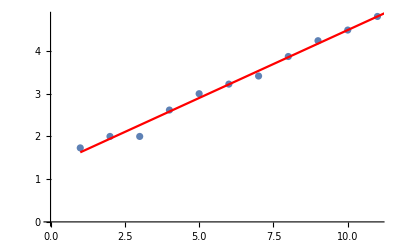

```mathematica
Show[ListPlot[Table[r[i],{i,2,12}]],Plot[g[x],{x,1,13},PlotStyle->Red]]
```

```mathematica
M=Table[If[n==1,{{1,0},{0,1}}/r[m],{{Cos[2*Pi/m],-Sin[2*Pi/m]},{Sin[2*Pi/m],Cos[2*Pi/m]}}],{n,1,12}];
```

```mathematica
in=Table[If[n==1,{0,0},{-1/2,Sqrt[3]/2}],{n,1,12}];
```

```mathematica
f[j_,{x_,y_}] :=M[[j]]. {x,y}+in[[j]]
```

```mathematica
pt={0.01,0.01};
cr[n_]:=cols[[n]];
```

```mathematica
aa=ParallelTable[pt=f[dlst[[j]],pt],{j,Length[dlst]}];
```

```mathematica
g0=ListPlot[aa,AspectRatio->Automatic,ColorFunction->Hue,PlotStyle->{PointSize[0.0005]},ImageSize->{2000,2000},PlotRange->All,Axes->False,Background->Black];
```

```mathematica
ptlst=Point[Developer`ToPackedArray[aa],VertexColors->Developer`ToPackedArray[cr/@dlst]];
```

```mathematica
g2=Show[Graphics[{PointSize[.001],ptlst}],AspectRatio->Automatic,PlotRange->All,ImageSize->{2000,2000},Background->Black];
```

```mathematica
Export["IFS_12part_Sierpinski_Overlap_2000000.jpg",{g0,g2}]
```

IFS_12part_Sierpinski_Overlap_2000000.jpg

```mathematica
(*end*)
```